```mathematica
z[α_, R0_] := R0^(1/α) - 1;
cv2[ψ_, p_, α_, R0_] := (p ((1 + z[α, R0])^2/(1 + 2 z[α, R0]))^((1 - ψ) α))/(1 - ((1 + z[α, R0])/(1 + 2 z[α, R0]))^α) - 1;
```

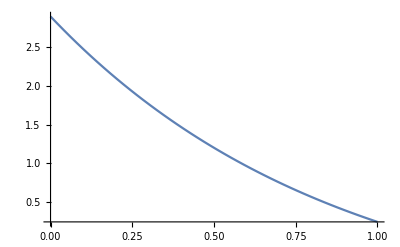

```mathematica
Plot[cv2[ψ, 1 - 1/12, 3, 12],{ψ, 0, 1}, PlotRange->All]
```